```mathematica
SetDirectory["/Users/eduardolandulfo/Documents/ANLYSIS"]
```

/Users/eduardolandulfo/Documents/ANLYSIS

```mathematica
FileNames[]
```

{160801_160930_Sao_Paulo.txt,160816_161231_Sao_Paulo.txt,1-s2.0-S1875963713000736-main.pdf,AERONET_SD.nb,SN7.pdf}

```mathematica
MS=Import["160801_160930_Sao_Paulo.txt","Data"];
```

```mathematica
MS[[1;;4]];
```

```mathematica
VX=Length[MS];
```

```mathematica
SIZE=Table[{ToExpression[StringTake[StringDrop[MS[[i]],43],8]],ToExpression[StringTake[StringDrop[MS[[i]],52],8]],ToExpression[StringTake[StringDrop[MS[[i]],61],8]],ToExpression[StringTake[StringDrop[MS[[i]],70],8]],ToExpression[StringTake[StringDrop[MS[[i]],79],8]],ToExpression[StringTake[StringDrop[MS[[i]],88],8]],ToExpression[StringTake[StringDrop[MS[[i]],97],8]],ToExpression[StringTake[StringDrop[MS[[i]],106],8]],ToExpression[StringTake[StringDrop[MS[[i]],115],8]],ToExpression[StringTake[StringDrop[MS[[i]],124],8]],ToExpression[StringTake[StringDrop[MS[[i]],133],8]],ToExpression[StringTake[StringDrop[MS[[i]],142],8]],ToExpression[StringTake[StringDrop[MS[[i]],151],8]],ToExpression[StringTake[StringDrop[MS[[i]],160],8]],ToExpression[StringTake[StringDrop[MS[[i]],169],8]],ToExpression[StringTake[StringDrop[MS[[i]],178],8]],ToExpression[StringTake[StringDrop[MS[[i]],187],8]],ToExpression[StringTake[StringDrop[MS[[i]],196],8]],ToExpression[StringTake[StringDrop[MS[[i]],205],8]],ToExpression[StringTake[StringDrop[MS[[i]],214],8]],ToExpression[StringTake[StringDrop[MS[[i]],223],8]],ToExpression[StringTake[StringDrop[MS[[i]],233],8]]} ,{i,4,4}];
```

```mathematica
SM=Table[{ToExpression[StringTake[StringDrop[MS[[i]],31],8]],ToExpression[StringTake[StringDrop[MS[[i]],40],8]],ToExpression[StringTake[StringDrop[MS[[i]],49],8]],ToExpression[StringTake[StringDrop[MS[[i]],58],8]],ToExpression[StringTake[StringDrop[MS[[i]],67],8]],ToExpression[StringTake[StringDrop[MS[[i]],76],8]],ToExpression[StringTake[StringDrop[MS[[i]],85],8]],ToExpression[StringTake[StringDrop[MS[[i]],94],8]],ToExpression[StringTake[StringDrop[MS[[i]],103],8]],ToExpression[StringTake[StringDrop[MS[[i]],112],8]],ToExpression[StringTake[StringDrop[MS[[i]],121],8]],ToExpression[StringTake[StringDrop[MS[[i]],130],8]],ToExpression[StringTake[StringDrop[MS[[i]],139],8]],ToExpression[StringTake[StringDrop[MS[[i]],148],8]],ToExpression[StringTake[StringDrop[MS[[i]],157],8]],ToExpression[StringTake[StringDrop[MS[[i]],166],8]],ToExpression[StringTake[StringDrop[MS[[i]],175],8]],ToExpression[StringTake[StringDrop[MS[[i]],184],8]],ToExpression[StringTake[StringDrop[MS[[i]],193],8]],ToExpression[StringTake[StringDrop[MS[[i]],202],8]],ToExpression[StringTake[StringDrop[MS[[i]],211],8]],ToExpression[StringTake[StringDrop[MS[[i]],220],8]],ToExpression[StringTake[StringDrop[MS[[i]],229],8]]} ,{i,5,VX}];
```

```mathematica
DIST=Table[Table[{SIZE[[1,i]],SM[[j,i]]},{i,1,22}],{j,1,60}];
SD=Table[Interpolation[DIST[[i]]],{i,1,60}];(* Interpolação dos dados x tamanho (DIST X SD) Só assim pode-se fazer o PLOT*)
```

```mathematica
AH=StringJoin[ToString[TIMET1[[3,3]]],"/",ToString[TIMET1[[3,2]]],"/",ToString[TIMET1[[3,1]]]](*ESCREVER A DATA*)
```

17/8/2016

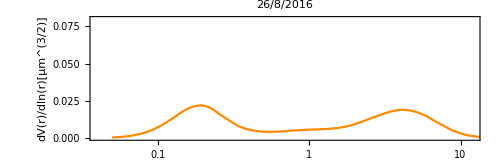

```mathematica
LogLinearPlot[{SD[[07]][x]}, {x,0.05,15},Frame->True,PlotStyle->{Table[Hue[i 0.09/5],{i,1,5}],Dashed,Dashed,Dashed},PlotLegends->"Placeholder",PlotRange-> {{0.04,12},{0.0001,0.08}},AspectRatio-> 1/3,FrameLabel-> {"Radius[µm]", "dV(r)/dln(r)[µm^(3/2)]"},LabelStyle->Directive[Bold,FontFamily->"Helvetica",FontSize->16],PlotLabel->AH[[6]],FrameStyle->Directive[ Thick],ImageSize-> 500]
```

```mathematica
TIMET1=Table[{ToExpression[StringTake[StringDrop[MS⟦i⟧,6],4]],ToExpression[StringTake[StringDrop[MS⟦i⟧,3],2]],ToExpression[StringTake[MS⟦i⟧,2]],ToExpression[StringTake[StringDrop[MS⟦i⟧,11],2]],ToExpression[StringTake[StringDrop[MS⟦i⟧,14],2]],ToExpression[StringTake[StringDrop[MS⟦i⟧,17],2]]},{i,5,VX}];
```

```mathematica
TIMETT=Table[{DateList[TIMET1⟦i⟧],SM[[i,1]]},{i,1,60}];(*EXEMPLO DE VETOR*)
```

```mathematica
DIAS=GatherBy[Partition[TIMET1,1],#[[1,1;;3]]&][[All,All,1]];
```

```mathematica
UV=Gather[TIMETT,#1[[1,1;;3]]==#2[[1,1;;3]]&];(*Let's unpack this single-liner.Partition just organises the data into date-value pairs.The GatherBy statement then groups each of these pairs if the first few elements of the date are the same.The specification 1;;3 covers daily data.If you wanted monthly averages you would use 1;;2 instead. The[[All,All,2]] bit just ensures that you are only operating on the values,not the dates https://mathematica.stackexchange.com/questions/48170/how-to-mean-of-day-month-value*)
```

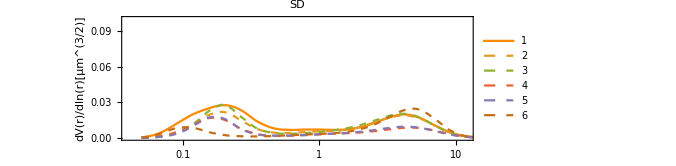

```mathematica
LogLinearPlot[{SD[[6]][x],SD[[7]][x],SD[[8]][x],SD[[9]][x],SD[[10]][x],SD[[11]][x]}, {x,0.05,15},Frame->True,PlotStyle->{Table[Hue[i 0.09/5],{i,1,5}],Dashed,Dashed,Dashed,Dashed,Dashed},PlotLegends->"Placeholder",PlotRange-> {{0.04,12},{0.0001,0.10}},AspectRatio-> 1/3,FrameLabel-> {"Radius[µm]", "dV(r)/dln(r)[µm^(3/2)]"},LabelStyle->Directive[Bold,FontFamily->"Helvetica",FontSize->16],PlotLabel->"SD",FrameStyle->Directive[ Thick],ImageSize-> 500]
```

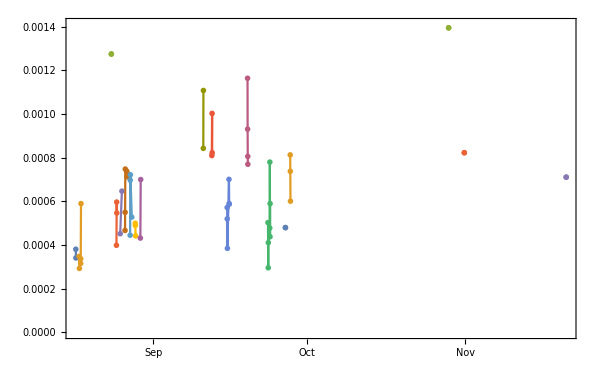

```mathematica
DateListPlot[UV,PlotTheme->"OpenMarkers",ImageSize->600]
```

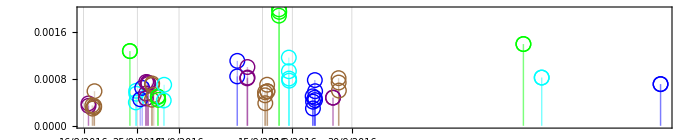

```mathematica
DateListPlot[UV,Joined->False,Filling->Axis,ImageSize->700,AspectRatio->1/5,FrameLabel->Automatic,Joined-> False,PlotStyle->{Purple,Brown,Green,Cyan,Blue},PlotRange-> All,PlotMarkers-> {○,15},AspectRatio->1/3,ImageSize->1000,GridLines-> {Automatic,None},DateTicksFormat->{"Day","/","MonthShort","/","Year"},FrameTicks->{{Automatic,Automatic},{{"Sep 20, 2016","Sep 30, 2016","Sep 15, 2016","Sep 1, 2016","Aug 25, 2016","Aug 16, 2016"},Automatic}}]
```